# Fig3

## green function

### geo

```mathematica
a1={Sqrt[3]/2,-1/2};a2={Sqrt[3]/2,1/2};
b6={2*Pi/Sqrt[3],-2*Pi};b2={2*Pi/Sqrt[3],2*Pi};
Simplify[a1.b6];
Simplify[a2.b6];
Simplify[a1.b2];
Simplify[a2.b2];
kG={0,0}.{b6,b2};
kM={0,1/2}.{b6,b2};
kK={1/3,2/3}.{b6,b2};
```

```mathematica
kM
```

{π/(√3),π}

```mathematica
kK//Norm
```

(4 π)/3

```mathematica
a1//Norm
```

1

```mathematica
a1.b3
```

{(√3)/2,-1/2}.b3

```mathematica
a1.b2
```

0

```mathematica
a2.b
```

{(√3)/2,1/2}.b

```mathematica
b1=b6+b2;b4=-b1;b3=-b6;b5=-b2;
```

```mathematica
b={b1,b2,b3,b4,b5,b6};
```

```mathematica
gg2[ θ_]:=(θ 4π)/(√3){(√3)/2,-1/2};gg3[ θ_]:=(θ 4π)/(√3){(√3)/2,1/2};gg1 [ θ_]=gg2[ θ]-gg3[ θ];gg4[ θ_]:=-gg1[ θ];gg5[ θ_]=-gg2[ θ];gg6[ θ_]=-gg3[ θ];
```

```mathematica
bb={b2+b3,b3+b4,b4+b5,b5+b6,b6+b1,b1+b2}
```

{{0,4 π},{-2 √3 π,2 π},{-2 √3 π,-2 π},{0,-4 π},{2 √3 π,-2 π},{2 √3 π,2 π}}

```mathematica
{gg1[1],gg2[1],gg3[1],gg4[1],gg5[1],gg6[1]}
```

{{0,-(4 π)/(√3)},{2 π,-(2 π)/(√3)},{2 π,(2 π)/(√3)},{0,(4 π)/(√3)},{-2 π,(2 π)/(√3)},{-2 π,-(2 π)/(√3)}}

```mathematica
TA=5Pi/180;
```

```mathematica
gg2[TA]//Norm
```

π^2/(9 √3)

```mathematica
mkK= {TA 4 π/3, 0};mkM=TA{π,-π/(√3)};mkG={0,0};
```

```mathematica
aM1={1,0};
```

```mathematica
aM2=RotationMatrix[2Pi/6].{1,0};
```

```mathematica
Solve[{{x,y}.aM2==2Pi,{x,y}.aM1==0},{x,y}]
```

{{x→0,y→(4 π)/(√3)}}

```mathematica
bM1={1,-1/Sqrt[3]};bM2={0,2/Sqrt[3]}
```

{0,2/(√3)}

```mathematica
bM1//Norm
```

2/(√3)

### ham

```mathematica
PauliMatrix[1]
```

{{0,1},{1,0}}

```mathematica
A=0.365;B=-0.706;D2=-0.532
```

-0.532

```mathematica
A=0.365;B=-0.706;D2=-0.532;HBHZ[{kx_,ky_},M_]:=A( kx PauliMatrix[1]- ky PauliMatrix[2]) +(M-B(kx^2+ky^2)) PauliMatrix[3]-D2(kx^2+ky^2) PauliMatrix[0]
```

```mathematica
HBHZT[{kx_,ky_},M_]:=ArrayFlatten@DiagonalMatrix[Unevaluated@{HBHZ[{kx,ky},M],HBHZ[-{kx,-ky},M]}]+100 IdentityMatrix[4]
```

### spectrum function

```mathematica
n=40;
Glength=Join[Table[i,{i,n+1,2n}],{2n+1},Table[i,{i,2n,n+1,-1}]];
Gbegin=Table[Total@Glength[[1;;i]]-Glength[[i]]+1,{i,1,Length[Glength]}];G[th_]:=Join[ArrayFlatten[Table[(n-i)gg5[th]+j gg1[th],{i,0,n},{j,-i,n}],1],ArrayFlatten[Table[(-i)gg5[th]+j gg1[th],{i,1,n},{j,-n,n-i}],1]];
{Total@Glength}
```

{4921}

```mathematica
A1=Flatten[{x,y}/.Solve[{{x,y}.gg1[TA]==2Pi,{x,y}.gg2[TA]==0},{x,y}]];A2=Flatten[{x,y}/.Solve[{{x,y}.gg2[TA]==2Pi,{x,y}.gg1[TA]==0},{x,y}]];
```

```mathematica
SelectG[g_List]:=If[Norm[g]<=Norm[23gg1[TA]],g,Null]
```

```mathematica
SelectG[G[TA][[1]]]
```

```mathematica
GTA=DeleteCases[Map[SelectG,G[TA]],Null];
```

```mathematica
b1moire[T_]:=gg3[T]
```

```mathematica
DOmega=π^2/18*π^2/(18 √3)*2
```

π^4/(162 √3)

```mathematica
nA=0.365;nB=-0.706;nD2=-0.532;
fund0[{kx_,ky_},D2_]:=-D2(kx^2+ky^2);
fundx[kx_,A_]:=A kx;
fundy[ky_,A_]:=-A ky;
fundz[{kx_,ky_},M_,B_]:=M-B(kx^2+ky^2);
HBHZgreen[{kx_,ky_},M_,A_,B_,D2_]:=fundx[kx,A] PauliMatrix[1]+fundy[ky,A] PauliMatrix[2]+fundz[{kx,ky},M,B] PauliMatrix[3] +fund0[{kx,ky},D2]PauliMatrix[0];
```

```mathematica
Greefunction00[{kx_,ky_},M_,A_,B_,D2_,E_,eps_]:=((E+I eps)PauliMatrix[0]-fund0[{kx,ky},D2]PauliMatrix[0]+fundx[kx,A] PauliMatrix[1]+fundy[ky,A] PauliMatrix[2]+fundz[{kx,ky},M,B] PauliMatrix[3])/((E+I eps-fund0[{kx,ky},D2])^2-(fundx[kx,A]^2+fundy[ky,A]^2+fundz[{kx,ky},M,B]^2))
```

```mathematica
Greefunction022[{kx_,ky_},M_,A_,B_,D2_,e_,eps_]:=INT02/.{kxx->kx,kyy->ky,MM->M,AA->A,BB->B,DD2->D2,ee->e,eeps->eps}
```

```mathematica
INT0022[MM_,eeps_,{{kxx_,kyy_},ee_}]:=Total@Table[With[{t=Greefunction00[{kxx,kyy}+GTA[[i]],MM,nA,nB,nD2,ee,eeps]},{t.t,t}],{i,1,Dimensions[GTA]//First}]//Chop
```

```mathematica
GreenfunctionTraceint[v_,{a_List,b_List}]:=-2Im@Tr[b+v a.Inverse[IdentityMatrix[2]-v b]]
```

```mathematica
Traceofgreen[MM_,vv_,eeps_,{{kxx_,kyy_},ee_}]:=With[{test=INT0022[MM,eeps,{{kxx,kyy},ee}]},GreenfunctionTraceint[vv,test]]
```

```mathematica
neps=0.005;
```

```mathematica
INT0022[0.1,neps,{{0,0},0.01}]//Chop//MatrixForm
```

((151.908+13.4947 ⅈ
0) | (0
326.885-13.5102 ⅈ)
(-54.8325-0.763371 ⅈ
0) | (0
273.518-1.63663 ⅈ))

```mathematica
Traceofgreen[0.1,0.00385,neps,{{0,0},0.0601}]//AbsoluteTiming
```

{0.326884,407.797}

```mathematica
kpath1=Join[ Table[-L mkM,{L,1,0,-0.05}], Table[L mkK,{L,0.05,1,0.05}]];Eng=Range[0,0.30,0.0015];paraspace=Flatten[Table[{kpath1[[i]],Eng[[j]]},{i,1,Length@kpath1},{j,1,Length@Eng}],1];paraspace0=Flatten[Table[{i,Eng[[j]]},{i,1,Length@kpath1},{j,1,Length@Eng}],1];
```

```mathematica
result00=ParallelTable[Traceofgreen[0.1,0.00385,neps,p],{p,paraspace}];//Chop
```

```mathematica
selectregion[{a_,b_,c_}]:=If[b<=0.24,{a,b,c}];
```

```mathematica
ListDensityPlot[DeleteCases[Map[selectregion,Map[Flatten,Transpose@{paraspace0,result00}]],Null],PlotRange->All,ColorFunction->"Rainbow",PlotLegends->Automatic,FrameLabel->{"Momentum","E (eV)"},FrameTicks->{{Automatic,None},{{{1,"Γ"},{11,"K"},{21,"M"},{31,"Γ"}},None}},PlotLabel->"Spectrum function",PlotRange->All,FrameTicksStyle->Directive[Black,20],FrameStyle->Directive[Black,20],LabelStyle->Directive[Black,20]]
```

```mathematica
result01=ParallelTable[Traceofgreen[0.1,0.00405,neps,p],{p,paraspace}];//Chop
```

```mathematica
ListDensityPlot[DeleteCases[Map[selectregion,Map[Flatten,Transpose@{paraspace0,result01}]],Null],PlotRange->All,ColorFunction->"Rainbow",PlotLegends->Automatic,FrameLabel->{"Momentum","E (eV)"},FrameTicks->{{Automatic,None},{{{1,"Γ"},{11,"K"},{21,"M"},{31,"Γ"}},None}},PlotLabel->"Spectrum function",PlotRange->All,FrameTicksStyle->Directive[Black,20],FrameStyle->Directive[Black,20],LabelStyle->Directive[Black,20]]
```

### raw data

```mathematica
data0=
```

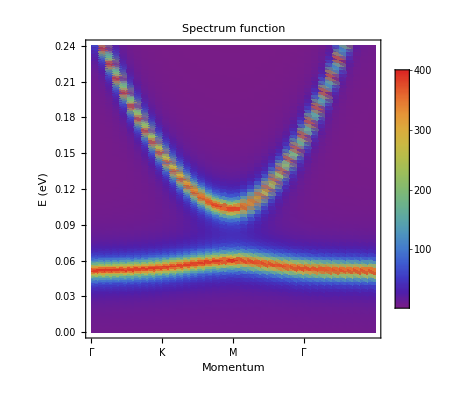

```mathematica
ListDensityPlot[data0,PlotRange->All,ColorFunction->"Rainbow",PlotLegends->Automatic,FrameLabel->{"Momentum","E (eV)"},FrameTicks->{{Automatic,None},{{{1,"Γ"},{11,"K"},{21,"M"},{31,"Γ"}},None}},PlotLabel->"Spectrum function",PlotRange->All,FrameTicksStyle->Directive[Black,20],FrameStyle->Directive[Black,20],LabelStyle->Directive[Black,20]]
```

```mathematica
data1=
```

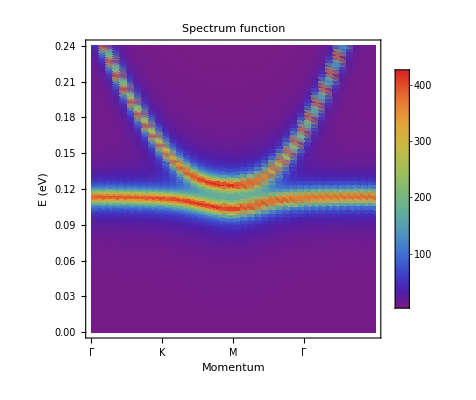

```mathematica
ListDensityPlot[data1,PlotRange->All,ColorFunction->"Rainbow",PlotLegends->Automatic,FrameLabel->{"Momentum","E (eV)"},FrameTicks->{{Automatic,None},{{{1,"Γ"},{11,"K"},{21,"M"},{31,"Γ"}},None}},PlotLabel->"Spectrum function",PlotRange->All,FrameTicksStyle->Directive[Black,20],FrameStyle->Directive[Black,20],LabelStyle->Directive[Black,20]]
```

## THF

```mathematica
a=1.238;c=0.119
```

```mathematica
E1[L_]:=c^2/a L
```

```mathematica
H[{kx_,ky_},L_]:={{1000+a kx^2+a ky^2,c (kx+ I ky )},{c(kx- I ky),E1[L]+1000}}
```

```mathematica
BW[L_]:=Abs@First[Eigenvalues[H[{0,0},L],-1]-Eigenvalues[H[mkK,L],-1]]
```

```mathematica
BWG[L_]:=If[L<=2,BW[L]/Sqrt[(c^4 L^2)/a^2],BW[L]/Sqrt[(4 c^4 (-1+L))/a^2]]
```

```mathematica
P0=Plot[Abs@BWG[L],{L,0.2,5},PlotRange->{0,1},PlotStyle->Red,Frame->True];
```

0.119

```mathematica
P1=Plot[{(2 √L)/(1+L)},{L,0.2,5},PlotRange->{0,1},PlotStyle->{Blue},Frame->True,FrameTicks->{{None,All},{None,None}}];
```

```mathematica
P2=Graphics[{Dashed,Red,Line[{{2,0},{2,1}}]}];
```

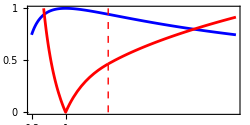

```mathematica
Show[P1,P0,P2,ImageSize->250,PlotRange->{{0.2,5},{0,1}},GridLines->{{{2,Directive[Red,Dashed]},{1,Directive[Red,Thick]},3 Pi},{{-1,Blue},-.5,.5,{1,Blue}}},Framed->True,BaseStyle->{FontSize->20,FontWeight->"Bold"},AspectRatio->0.5,FrameTicks->{{{0,0.5,1},{0,0.5,1}},{{{1,1},{5,5},{0.2,0.2},{3,3}},None}},FrameTicksStyle->{{Red,Blue},{Black,Green}}]
```